# Hints for a luminosity transition in the Cepheid SnIa calibrator data Leandros Perivolaropoulos and Foteini Skara The one dimensional relative probability density value for three cases (I,II,III) studied. All measurements are shown as normalized Gaussian distribution

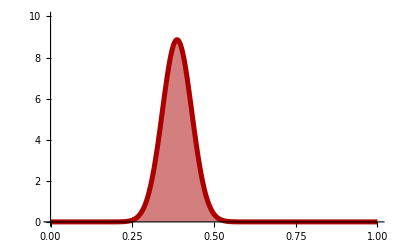

```mathematica
prs=Plot[PDF[NormalDistribution[0.387,0.045],x],{x,0,1},PlotRange->{{0,1},{0,10}},PlotStyle->{PointSize->Large,Thickness[0.009],Darker[Red]},FillingStyle->Directive[Opacity[0.5]],Filling->Axis]
```

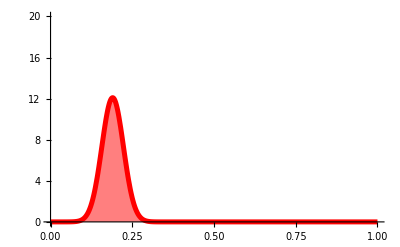

```mathematica
prl=Plot[PDF[NormalDistribution[0.190,0.033],x],{x,0,1},PlotRange->{{0,1},{0,20}},PlotStyle->{PointSize->Large,Thickness[0.009],Red},FillingStyle->Directive[Opacity[0.5]],Filling->Axis]
```

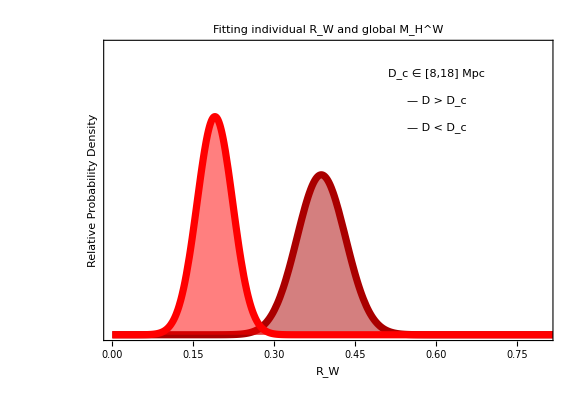

```mathematica
figpr=Show[prs,prl,Graphics[{Inset["D_c ∈ [8,18] Mpc",{0.6,14.5},BaseStyle->{Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset["— D > D_c",{0.6,13},BaseStyle->{Bold,Red,FontFamily->"Times",18}]}],Graphics[{Inset["— D < D_c",{0.6,11.5},BaseStyle->{Bold,Darker[Red],FontFamily->"Times",18}]}],
PlotRange->{{0,0.8},{0,16}},PlotLabel->"Fitting individual R_W and global M_H^W",LabelStyle->Directive[Bold,Italic,16,Black],FrameLabel->{"R_W","Relative Probability Density"},Frame->True,BaseStyle->{FontFamily->"Times",8},FrameStyle->Directive[Black,Thickness[0.007]],FrameTicks->{{None,None},{All,None}},PlotRangeClipping->True,AspectRatio->0.7,ImageSize->Large]
```

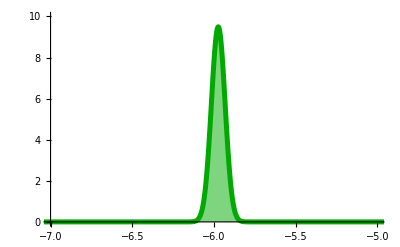

```mathematica
pms=Plot[PDF[NormalDistribution[-5.974,0.042],x],{x,-10,0},PlotRange->{{-7,-5},{0,10}},PlotStyle->{PointSize->Large,Thickness[0.009],Darker[Green]},FillingStyle->Directive[Opacity[0.5]],Filling->Axis]
```

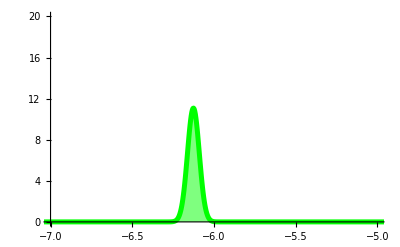

```mathematica
pml=Plot[PDF[NormalDistribution[-6.126,0.036],x],{x,-10,1},PlotRange->{{-7,-5},{0,20}},PlotStyle->{PointSize->Large,Thickness[0.009],Green},FillingStyle->Directive[Opacity[0.5]],Filling->Axis]
```

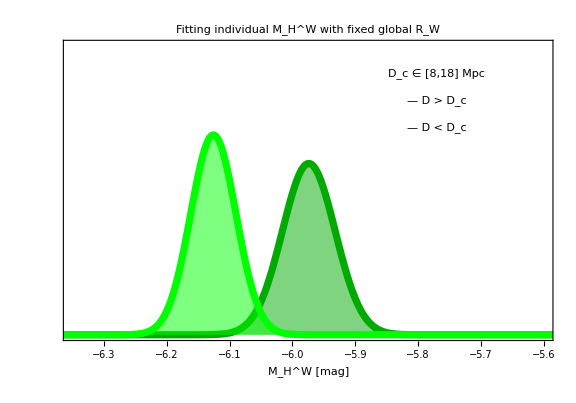

```mathematica
figpm=Show[pms,pml,Graphics[{Inset["D_c ∈ [8,18] Mpc",{-5.77,14.5},BaseStyle->{Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset["— D > D_c",{-5.77,13},BaseStyle->{Bold,Green,FontFamily->"Times",18}]}],Graphics[{Inset["— D < D_c",{-5.77,11.5},BaseStyle->{Bold,Darker[Green],FontFamily->"Times",18}]}],
PlotRange->{{-6.35,-5.6},{0,16}},PlotLabel->"Fitting individual M_H^W with fixed global  R_W",LabelStyle->Directive[Bold,Italic,16,Black],FrameLabel->{"M_H^W [mag]",""},Frame->True,BaseStyle->{FontFamily->"Times",8},FrameStyle->Directive[Black,Thickness[0.007]],FrameTicks->{{None,None},{All,None}},PlotRangeClipping->True,AspectRatio->0.7,ImageSize->Large]
```

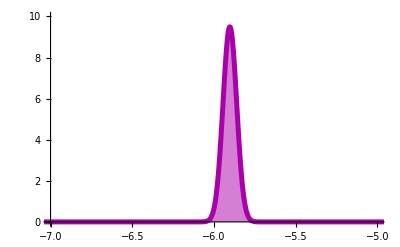

```mathematica
pmrs=Plot[PDF[NormalDistribution[-5.903,0.042],x],{x,-10,0},PlotRange->{{-7,-5},{0,10}},PlotStyle->{PointSize->Large,Thickness[0.009],Darker[Magenta]},FillingStyle->Directive[Opacity[0.5]],Filling->Axis]
```

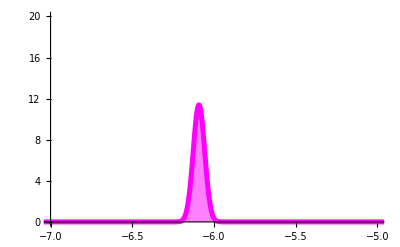

```mathematica
pmrl=Plot[PDF[NormalDistribution[-6.092,0.035],x],{x,-10,1},PlotRange->{{-7,-5},{0,20}},PlotStyle->{PointSize->Large,Thickness[0.009],Magenta},FillingStyle->Directive[Opacity[0.5]],Filling->Axis]
```

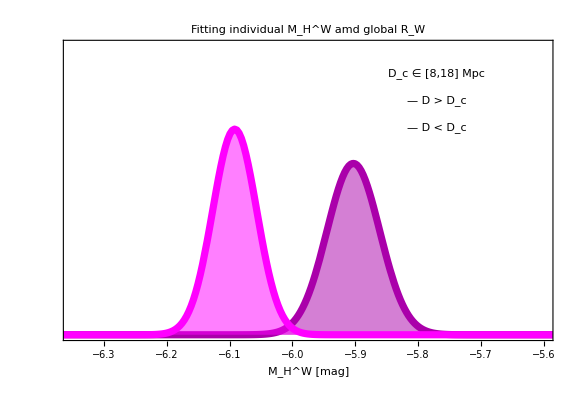

```mathematica
figpmr=Show[pmrs,pmrl,Graphics[{Inset["D_c ∈ [8,18] Mpc",{-5.77,14.5},BaseStyle->{Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset["— D > D_c",{-5.77,13},BaseStyle->{Bold,Magenta,FontFamily->"Times",18}]}],Graphics[{Inset["— D < D_c",{-5.77,11.5},BaseStyle->{Bold,Darker[Magenta],FontFamily->"Times",18}]}],
PlotRange->{{-6.35,-5.6},{0,16}},PlotLabel->"Fitting individual M_H^W amd global R_W",LabelStyle->Directive[Bold,Italic,16,Black],FrameLabel->{"M_H^W  [mag]",""},Frame->True,BaseStyle->{FontFamily->"Times",8},FrameStyle->Directive[Black,Thickness[0.007]],FrameTicks->{{None,None},{All,None}},PlotRangeClipping->True,AspectRatio->0.7,ImageSize->Large]
```

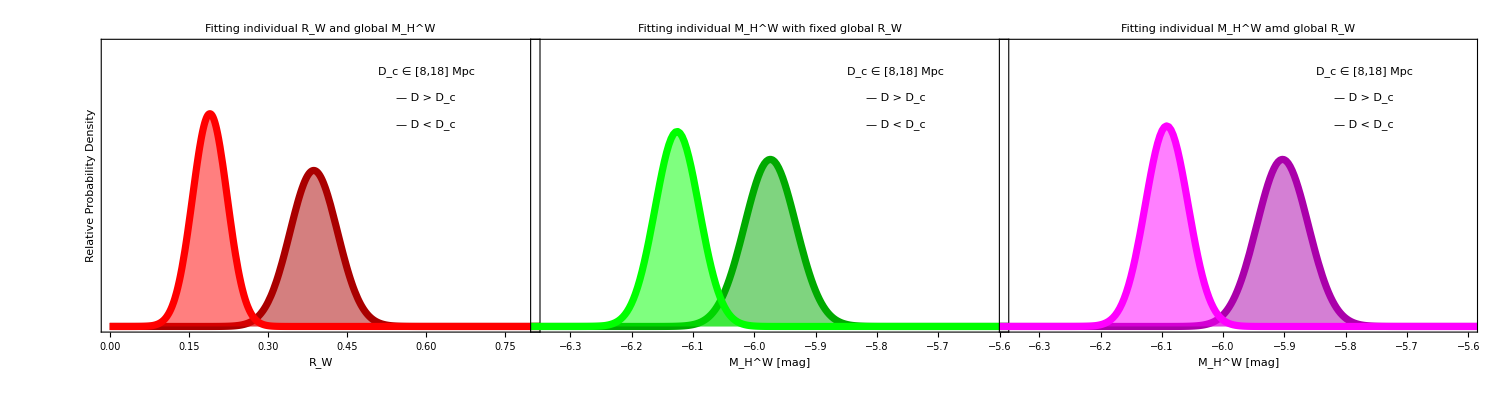

```mathematica
figprob=GraphicsGrid[{{figpr,figpm,figpmr}},ImageSize->1500,Spacings->-96,AspectRatio->Automatic]
```

```mathematica
Export[NotebookDirectory[]<>"figprob.pdf",figprob,ImageResolution->1000];
```